```mathematica
1+1
```

2

```mathematica
Needs["PyTools`Symbolic`"]
```

```mathematica
replRational=Rational[x_Integer, y_Integer]-> 1.0`16x/ y;
parTimesRule=(Times->parTimes);
parPowerRule= (Power -> parPower);
(*parSin=(Sin[x_]->parSin[x]);
parCos=(Cos[x_]->parCos[x]);*)
parRules={parTimesRule, parPowerRule} ;
```

## Use with autograd

```mathematica
Remove[b, cm]
b[t_, seed_]:=Module[{size=4, thetas, b},
SeedRandom[seed];
thetas=Outer[RandomChoice[{t, -t, 95/100+(-99-95)/100/2(t+1), 1, -1}] &, Range[size], Range[size - 1], 1, 1];
b=Outer[If[#2 < size, Cos[thetas[[#1, #2]]] (Times @@ Sin[thetas[[#1, 1 ;; #2 - 1]]]),
          Times @@ Sin[thetas[[#1, 1 ;; #2 - 1]]]] &, Range[size], Range[size], 1, 1];
b
]
cm[t_, seed_]:=Module[{size=4, thetas, b},
SeedRandom[seed];
thetas=Outer[RandomChoice[{t, -t, 95/100+(-99-95)/100/2(t+1), 1, -1}] &, Range[size], Range[size - 1], 1, 1];
b=Outer[If[#2 < size, Cos[thetas[[#1, #2]]] (Times @@ Sin[thetas[[#1, 1 ;; #2 - 1]]]),
          Times @@ Sin[thetas[[#1, 1 ;; #2 - 1]]]] &, Range[size], Range[size], 1, 1];
Dot[b, Transpose[b]]
]
```

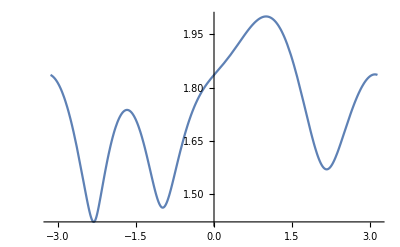

```mathematica
Plot[Norm[b[t, 130]], {t, -Pi, Pi}]
```

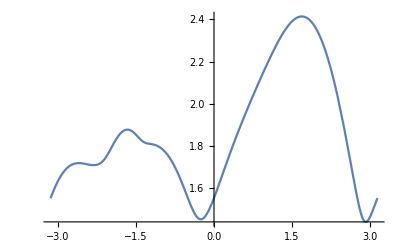

```mathematica
With[{local=D[b[t, 130], t]},
Plot[Norm[local], {t, -Pi, Pi}]
]
```

```mathematica
With[{expr=cm[t, 132] /.replRational},
ToSymbolicPython[expr ] 
] //ToPython
```

import math
[ [ math.cos(1)**2+math.cos(1)**2*math.sin(1)**2+math.cos(1)**2*math.sin(1)**4+math.sin(1)**6, math.cos(1)**2+-1*math.cos(1)**2*math.sin(1)**2+math.cos(1)*math.cos(0.95+-0.97*1+t)*math.sin(1)**4+math.sin(1)**5*math.sin(0.95+-0.97*1+t), math.cos(1)**2+-1*math.cos(1)*math.cos(t)*math.sin(1)**2+-1*math.cos(1)*math.cos(t)*math.sin(1)**3*math.sin(t)+math.sin(1)**4*math.sin(t)**2, math.cos(1)**2+math.cos(1)**2*math.sin(1)**2+-1*math.cos(1)**2*math.sin(1)**4+-1*math.sin(1)**6 ], [ math.cos(1)**2+-1*math.cos(1)**2*math.sin(1)**2+math.cos(1)*math.cos(0.95+-0.97*1+t)*math.sin(1)**4+math.sin(1)**5*math.sin(0.95+-0.97*1+t), math.cos(1)**2+math.cos(1)**2*math.sin(1)**2+math.cos(0.95+-0.97*1+t)**2*math.sin(1)**4+math.sin(1)**4*math.sin(0.95+-0.97*1+t)**2, math.cos(1)**2+math.cos(1)*math.cos(t)*math.sin(1)**2+-1*math.cos(t)*math.cos(0.95+-0.97*1+t)*math.sin(1)**3*math.sin(t)+math.sin(1)**3*math.sin(t)**2*math.sin(0.95+-0.97*1+t), math.cos(1)**2+-1*math.cos(1)**2*math.sin(1)**2+-1*math.cos(1)*math.cos(0.95+-0.97*1+t)*math.sin(1)**4+-1*math.sin(1)**5*math.sin(0.95+-0.97*1+t) ], [ math.cos(1)**2+-1*math.cos(1)*math.cos(t)*math.sin(1)**2+-1*math.cos(1)*math.cos(t)*math.sin(1)**3*math.sin(t)+math.sin(1)**4*math.sin(t)**2, math.cos(1)**2+math.cos(1)*math.cos(t)*math.sin(1)**2+-1*math.cos(t)*math.cos(0.95+-0.97*1+t)*math.sin(1)**3*math.sin(t)+math.sin(1)**3*math.sin(t)**2*math.sin(0.95+-0.97*1+t), math.cos(1)**2+math.cos(t)**2*math.sin(1)**2+math.cos(t)**2*math.sin(1)**2*math.sin(t)**2+math.sin(1)**2*math.sin(t)**4, math.cos(1)**2+-1*math.cos(1)*math.cos(t)*math.sin(1)**2+math.cos(1)*math.cos(t)*math.sin(1)**3*math.sin(t)+-1*math.sin(1)**4*math.sin(t)**2 ], [ math.cos(1)**2+math.cos(1)**2*math.sin(1)**2+-1*math.cos(1)**2*math.sin(1)**4+-1*math.sin(1)**6, math.cos(1)**2+-1*math.cos(1)**2*math.sin(1)**2+-1*math.cos(1)*math.cos(0.95+-0.97*1+t)*math.sin(1)**4+-1*math.sin(1)**5*math.sin(0.95+-0.97*1+t), math.cos(1)**2+-1*math.cos(1)*math.cos(t)*math.sin(1)**2+math.cos(1)*math.cos(t)*math.sin(1)**3*math.sin(t)+-1*math.sin(1)**4*math.sin(t)**2, math.cos(1)**2+math.cos(1)**2*math.sin(1)**2+math.cos(1)**2*math.sin(1)**4+math.sin(1)**6 ] ]

```mathematica
cm[0.5, 130] //MatrixForm
```

(1. | 0.842614 | 0.808273 | 0.843295
0.842614 | 1. | 0.971862 | 0.999998
0.808273 | 0.971862 | 1. | 0.971861
0.843295 | 0.999998 | 0.971861 | 1.)

```mathematica
Det[cm[1, 130]]
```

0

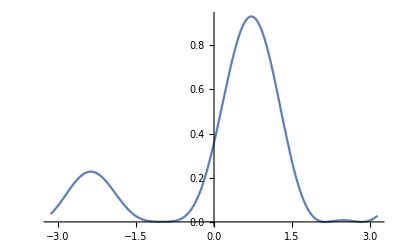

```mathematica
Plot[Det[cm[t, 132]], {t, -Pi, Pi}]
```

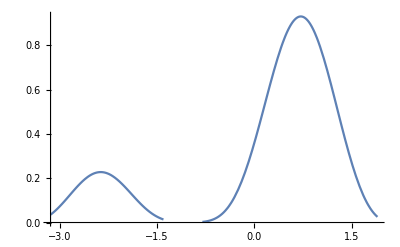

```mathematica
Show[Plot[Det[cm[t, 132]], {t, -Pi, -1.4}], Plot[Det[cm[t, 132]], {t, -0.8, 1.9}], PlotRange->All]
```

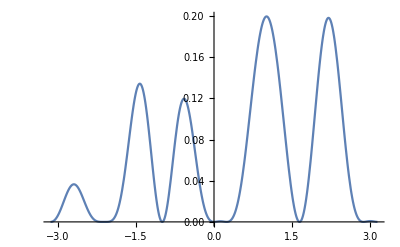

```mathematica
Plot[Det[cm[t, 133]], {t, -Pi, Pi}]
```

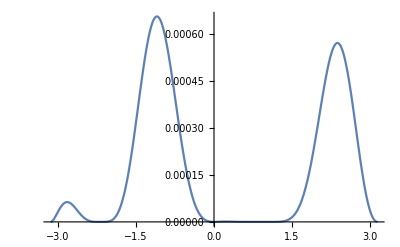

```mathematica
Plot[Det[cm[t, 140]], {t, -Pi, Pi}]
```

```mathematica
Reduce[Det[cm[t]]>0 && -1<t<1, t, Reals]
```

False

```mathematica
makeSqrt[vol1_, vol2_, rho_]:=MatrixFunction[Sqrt, {{vol1 vol1, rho vol1 vol2}, {rho vol1 vol2, vol2 vol2}}]
```

```mathematica
makeSqrt[0.22, 0.3, -0.98]
```

{{0.151639,-0.159392},{-0.159392,0.254154}}

```mathematica
MatrixForm /@ (D[makeSqrt[vol1, vol2, rho],# ] & /@ {vol1, vol2, rho}) /. {vol1->0.22, vol2->0.3, rho->-0.98}
```

{(0.973847 | -0.45377
-0.45377 | -0.28458),(-0.208692 | -0.198541
-0.198541 | 1.05587),(0.501662 | 0.47726
0.47726 | 0.299312)}

```mathematica
MatrixForm /@ (D[makeSqrt[vol1, vol2, rho],# ] & /@ {vol1, vol2, rho}) /. {vol1->1, vol2->1, rho->-0.98}
```

{(1.0329 | -0.316426
-0.316426 | -0.258631),(-0.258631 | -0.316426
-0.316426 | 1.0329),(1.5901 | 1.94543
1.94543 | 1.5901)}

```mathematica
With[{vol1=0.22, vol2=0.3, rho=-0.98},
MatrixFunction[Sqrt, {{vol1 vol1, rho vol1 vol2}, {rho vol1 vol2, vol2 vol2}}]
]
```

{{0.151639,-0.159392},{-0.159392,0.254154}}

```mathematica
D[MatrixFunction[Sqrt, {{vol1 vol1, rho vol1 vol2}, {rho vol1 vol2, vol2 vol2}}],vol1] /. {vol1->0.22, vol2->0.3, rho->-0.98}
```

{{0.973847,-0.45377},{-0.45377,-0.28458}}

```mathematica
D[MatrixFunction[Sqrt, {{vol1 vol1, rho vol1 vol2}, {rho vol1 vol2, vol2 vol2}}],vol2] /. {vol1->0.22, vol2->0.3, rho->-0.98}
```

{{-0.208692,-0.198541},{-0.198541,1.05587}}

```mathematica
D[MatrixFunction[Sqrt, {{vol1 vol1, rho vol1 vol2}, {rho vol1 vol2, vol2 vol2}}],rho] /. {vol1->0.22, vol2->0.3, rho->-0.98}
```

{{0.501662,0.47726},{0.47726,0.299312}}

```mathematica
CholeskyDecomposition[cm[1.23, 130]]//MatrixForm
```

(1. | 0.958879 | 0.936219 | 0.960964
0. | 0.283817 | 0.277955 | 0.276455
0. | 0. | 0.215025 | -0.0000310823
0. | 0. | 0. | 0.011004)

```mathematica
Inverse[CholeskyDecomposition[cm[1.23, 130]]]//MatrixForm
```

(1. | -3.37851 | 0.0132784 | -2.44981
0. | 3.5234 | -4.55457 | -88.5319
0. | 0. | 4.65063 | 0.0131364
0. | 0. | 0. | 90.8763)

```mathematica
Module[{b=CholeskyDecomposition[cm[1.23, 130]], ub, varsy, varsz},
ub={x1, x2, x3, x4};
varsy={y1, y2, y3, y4};
varsz={z1, z2, z3, z4};
Reduce[Thread[Dot[Inverse[b],varsz]≤ub], varsz, Reals]
]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(z1<3.34806×10^-71 (2.9868×10^70 x1+2.86398×10^70 x2+2.7963×10^70 x3+2.87021×10^70 x4)&&((z2==1.12626×10^-55 (-2.63608×10^54 x1-7.68526×10^51 x2-7.85495×10^52 x4+2.63608×10^54 z1)&&z3==1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(1.12626×10^-55 (-2.63608×10^54 x1-7.68526×10^51 x2-7.85495×10^52 x4+2.63608×10^54 z1)<z2≤9.39869×10^-50 (-3.14925×10^48 x1+8.99171×10^45 x3-8.48975×10^46 x4+3.14925×10^48 z1)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3≤1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)<z3<2.1015×10^-29 (3.58363×10^30 x1+9.66061×10^28 x4-3.58363×10^30 z1+1.21073×10^31 z2)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤0.011004 x4)||(z3==2.1015×10^-29 (3.58363×10^30 x1+9.66061×10^28 x4-3.58363×10^30 z1+1.21073×10^31 z2)&&z4==2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3))))||(9.39869×10^-50 (-3.14925×10^48 x1+8.99171×10^45 x3-8.48975×10^46 x4+3.14925×10^48 z1)<z2<1.10446×10^-70 (-2.67993×10^69 x1+1.13553×10^63 x2+7.65282×10^66 x3-7.22444×10^67 x4+2.67993×10^69 z1)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3≤1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)<z3≤5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤0.011004 x4)||(5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)<z3<9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(z3==9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&z4==2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3))))||(1.10446×10^-70 (-2.67993×10^69 x1+1.13553×10^63 x2+7.65282×10^66 x3-7.22444×10^67 x4+2.67993×10^69 z1)≤z2<2.55554×10^-73 (-1.12573×10^72 x1+3.11507×10^70 x2+3.37215×10^70 x3-4.87452×10^66 x4+1.12573×10^72 z1)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3≤1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)<z3<5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤0.011004 x4)||(5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)≤z3<9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(z3==9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&z4==2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3))))||(z2==2.55554×10^-73 (-1.12573×10^72 x1+3.11507×10^70 x2+3.37215×10^70 x3-4.87452×10^66 x4+1.12573×10^72 z1)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3<1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(z3==1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)<z3<9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(z3==9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&z4==2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3))))||(2.55554×10^-73 (-1.12573×10^72 x1+3.11507×10^70 x2+3.37215×10^70 x3-4.87452×10^66 x4+1.12573×10^72 z1)<z2<6.83312×10^-64 (-4.21015×10^62 x1+1.1652×10^61 x2+1.26134×10^61 x3+4.21015×10^62 z1)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3<5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)≤z3≤1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)<z3<9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(z3==9.90059×10^-41 (1.16457×10^37 x1+2.17181×10^39 x3-1.16457×10^37 z1+3.93451×10^37 z2)&&z4==2.17516×10^-24 (-1.87662×10^23 x1+1.87662×10^23 z1-6.34019×10^23 z2+2.49186×10^21 z3))))||(z2==6.83312×10^-64 (-4.21015×10^62 x1+1.1652×10^61 x2+1.26134×10^61 x3+4.21015×10^62 z1)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3<5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)≤z3<1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(z3==1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))))||(6.83312×10^-64 (-4.21015×10^62 x1+1.1652×10^61 x2+1.26134×10^61 x3+4.21015×10^62 z1)<z2<1.25661×10^-47 (2.25859×10^46 x2+2.21194×10^46 x3+2.20001×10^46 x4)&&((z3==7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))||(7.11897×10^-32 (-3.08415×10^30 x2-3.00458×10^30 x4+1.08667×10^31 z2)<z3<5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤0.011004 x4)||(5.95895×10^-26 (3.60844×10^24 x3-5.21608×10^20 x4)≤z3<6.36767×10^-41 (5.01126×10^35 x2+3.37731×10^39 x3-1.76567×10^36 z2)&&1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3)≤z4≤8.05716×10^-15 (9.44805×10^15 x3-4.39394×10^16 z3))||(z3==6.36767×10^-41 (5.01126×10^35 x2+3.37731×10^39 x3-1.76567×10^36 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))))||(z2==1.25661×10^-47 (2.25859×10^46 x2+2.21194×10^46 x3+2.20001×10^46 x4)&&z3==6.36767×10^-41 (5.01126×10^35 x2+3.37731×10^39 x3-1.76567×10^36 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))))||(z1==3.34806×10^-71 (2.9868×10^70 x1+2.86398×10^70 x2+2.7963×10^70 x3+2.87021×10^70 x4)&&z2==2.55554×10^-73 (-1.12573×10^72 x1+3.11507×10^70 x2+3.37215×10^70 x3-4.87452×10^66 x4+1.12573×10^72 z1)&&z3==1.07007×10^-46 (6.70818×10^46 x1-1.85625×10^45 x2-6.70818×10^46 z1+2.33177×10^47 z2)&&z4==1.39875×10^-24 (-8.0753×10^21 x2+2.84525×10^22 z2-3.67795×10^22 z3))

```mathematica
Det[CholeskyDecomposition[cm[1.23, 130]]]
```

0.000671546

```mathematica
Det[cm[1.23, 130]]
```

4.50974×10^-7

## n=2

```mathematica
corrMat2={{1, ρ}, {ρ,1}};
vars={x1, x2};
exp=Dot[vars, Dot[Inverse[corrMat2], vars]];
simple=η x2^2;
```

```mathematica
Dot[Inverse[corrMat2], {x1, x2}]//Simplify
```

{(-x1+x2 ρ)/(-1+ρ^2),(-x2+x1 ρ)/(-1+ρ^2)}

```mathematica
Module[{rho, x1, x2, exp, res, aux},
rho=-0.95;
x1=1.;
x2=-2.;
exp=D[PDF[MultinormalDistribution[{0, 0}, corrMat2 /. ρ->aux], {x1, x2}], aux] /. aux->rho;
res=(--rho/(1-rho^2)+(x1-rho x2)/(1-rho^2)(-rho x1+x2)/(1-rho^2)) PDF[MultinormalDistribution[{0, 0}, corrMat2 /. ρ->rho], {x1, x2}] ;
{exp, res}
]
```

{0.097131,0.097131}

```mathematica
{lmat, umat}=With[{es=Eigensystem[Inverse@corrMat2]},
{DiagonalMatrix[es[[1]]],Transpose[#/Norm[#] & /@ es[[2]]]}
]
```

{{{(-1-ρ)/(-1+ρ^2),0},{0,(-1+ρ)/(-1+ρ^2)}},{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}}

```mathematica
umat //MatrixForm
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
lmat//Simplify
```

{{1/(1-ρ),0},{0,1/(1+ρ)}}

```mathematica
Dot[umat, Dot[lmat,Transpose[umat]]]-Inverse[corrMat2]//Simplify
```

{{0,0},{0,0}}

```mathematica
Thread[{lb1, lb2}≤ Dot[umat, {y1, y2}]≤{ub1, ub2}]
```

{lb1≤-y1/(√2)+y2/(√2)≤ub1,lb2≤y1/(√2)+y2/(√2)≤ub2}

```mathematica
Thread[{-Infinity, -Infinity}≤ {y1, y2}≤{x1, x2}]
```

{-∞≤y1≤x1,-∞≤y2≤x2}

```mathematica
Thread[{-Infinity, -Infinity}≤ Dot[Transpose[umat], {z1, z2}]≤ {x1, x2}]
```

{-∞≤-z1/(√2)+z2/(√2)≤x1,-∞≤z1/(√2)+z2/(√2)≤x2}

```mathematica
Reduce[Thread[{-Infinity, -Infinity}≤ Dot[Transpose[umat], {z1, z2}]≤ {x1, x2}], {z1, z2}]
```

(x1|x2)∈ℝ&&((z1≤(-x1+x2)/(√2)&&z2≤(2 x1+√2 z1)/(√2))||(z1>(-x1+x2)/(√2)&&z2≤(2 x2-√2 z1)/(√2)))

```mathematica
exp
```

x2 (x2/(1-ρ^2)-(x1 ρ)/(1-ρ^2))+x1 (x1/(1-ρ^2)-(x2 ρ)/(1-ρ^2))

```mathematica
D[Exp[-1/2 exp], ρ]//Simplify
```

(ⅇ^((x1^2+x2^2-2 x1 x2 ρ)/(2 (-1+ρ^2))) (-x1^2 ρ-x2^2 ρ+x1 x2 (1+ρ^2)))/((-1+ρ^2)^2)

```mathematica
Reduce[Thread[Dot[Transpose[umat], {z1, z2}]≤ {x1, x2}], {z1, z2}, Backsubstitution->True]
```

((x1|x2)∈ℝ&&z1≤-(x1-x2)/(√2)&&z2≤(2 x1+√2 z1)/(√2))||((x1|x2)∈ℝ&&z1>-(x1-x2)/(√2)&&z2≤-(-2 x2+√2 z1)/(√2))

```mathematica
Join[Thread[{lb1, lb2}≤ Dot[umat, {y1, y2}]≤{ub1, ub2}], Thread[{-Infinity, -Infinity}≤  {y1, y2}≤ {x1, x2}]]
```

{lb1≤-y1/(√2)+y2/(√2)≤ub1,lb2≤y1/(√2)+y2/(√2)≤ub2,-∞≤y1≤x1,-∞≤y2≤x2}

```mathematica
Reduce[Join[Thread[{lb1, lb2}≤ Dot[umat, {y1, y2}]≤{ub1, ub2}], Thread[{-Infinity, -Infinity}≤  {y1, y2}≤ {x1, x2}]], {lb1, lb2, ub1, ub2}]
```

(y1|y2)∈ℝ&&x2≥y2&&x1≥y1&&lb1≤1/2 (-√2 y1+√2 y2)&&lb2≤1/2 (√2 y1+√2 y2)&&ub1≥1/2 (-√2 y1+√2 y2)&&ub2≥1/2 (√2 y1+√2 y2)

```mathematica
Solve[Thread[Flatten[CoefficientList[exp-simple, vars]]==Flatten[CoefficientList[( x1-α x2)^2/β, vars]]], {α,β, γ, η}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{α→ρ,β→1-ρ^2,η→1}}

```mathematica
Reduce[{-Infinity<z2<b, -Infinity<√(1-ρ^2)z1 + ρ z2<a, -1<ρ<1}, {z1, z2}, Reals]
```

(a<0&&((-1<ρ<0&&((b≤a/ρ&&z1<-√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(b>a/ρ&&((z1≤0&&a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(0<z1<√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&a/ρ+√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)))))||(ρ==0&&z1<-√(a^2)&&z2<b)||(0<ρ<1&&((b<a/ρ&&((z1≤√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&z2<b)||(z1>√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&z2<a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2))))||(b==a/ρ&&((z1≤0&&z2<b)||(z1>0&&z2<a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2))))||(b>a/ρ&&((z1≤-√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&z2<b)||(-√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))<z1≤0&&z2<a/ρ+√((z1^2-z1^2 ρ^2)/ρ^2))||(z1>0&&z2<a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2))))))))||(a==0&&((-1<ρ<0&&((b<0&&z1<-√(-(b^2 ρ^2)/(-1+ρ^2))&&-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(b==0&&z1<0&&-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<0)||(b>0&&((z1≤0&&-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(0<z1<√(-(b^2 ρ^2)/(-1+ρ^2))&&√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)))))||(ρ==0&&z1<0&&z2<b)||(0<ρ<1&&((b<0&&((z1≤√(-(b^2 ρ^2)/(-1+ρ^2))&&z2<b)||(z1>√(-(b^2 ρ^2)/(-1+ρ^2))&&z2<-√((z1^2-z1^2 ρ^2)/ρ^2))))||(b==0&&((z1≤0&&z2<0)||(z1>0&&z2<-√((z1^2-z1^2 ρ^2)/ρ^2))))||(b>0&&((z1≤-√(-(b^2 ρ^2)/(-1+ρ^2))&&z2<b)||(-√(-(b^2 ρ^2)/(-1+ρ^2))<z1≤0&&z2<√((z1^2-z1^2 ρ^2)/ρ^2))||(z1>0&&z2<-√((z1^2-z1^2 ρ^2)/ρ^2))))))))||(a>0&&((-1<ρ<0&&((b<a/ρ&&z1<-√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(b==a/ρ&&z1<0&&a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(b>a/ρ&&((z1≤0&&a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)||(0<z1<√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&a/ρ+√((z1^2-z1^2 ρ^2)/ρ^2)<z2<b)))))||(ρ==0&&z1<√(a^2)&&z2<b)||(0<ρ<1&&((b<a/ρ&&((z1≤√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&z2<b)||(z1>√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&z2<a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2))))||(b==a/ρ&&((z1≤0&&z2<b)||(z1>0&&z2<a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2))))||(b>a/ρ&&((z1≤-√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))&&z2<b)||(-√((-a^2+2 a b ρ-b^2 ρ^2)/(-1+ρ^2))<z1≤0&&z2<a/ρ+√((z1^2-z1^2 ρ^2)/ρ^2))||(z1>0&&z2<a/ρ-√((z1^2-z1^2 ρ^2)/ρ^2))))))))

```mathematica
xxx=Reduce[{l2<z2<b, l1<onemr z1 + ρ z2<a, -1<r<1}, {z1, z2}, Reals];
```

```mathematica
xxx=Simplify[xxx /. onemr->√(1-r^2), Assumptions->{-1<r<1}];
```

```mathematica
xxx//Dimensions
```

{6}

```mathematica
xxx[[1]]
```

b>z2&&((b>0&&((a>0&&((l2<z2&&((a==√(1-r^2) z1+b ρ&&((a/(b-l2)==l1/(b-l2)+ρ&&((a+l1<0&&((a b)/l1==l2||(b l1)/a>l2||((a b)/l1>l2&&(b l1)/a<l2)||((a b)/l1<l2&&l2<0)))||((a b)/l1>l2&&(a+l1==0||(l1<0&&a+l1>0)))||(l1<0&&((a+l1>0&&((a b)/l1==l2||((a b)/l1<l2&&(b l1)/a>l2)||((b l1)/a<l2&&l2<0)))||(b>l2&&l2>0)))||(l2<0&&((a>l1&&l1>0)||(a+l1==0&&(a b)/l1<l2)))||(l2>0&&((a+l1≤0&&b>l2)||(a>l1&&l1>0&&(b l1)/a>l2)))))||(l1==0&&l2<0&&a/(b-l2)==ρ)))||(a/(b-l2)+ρ==l1/(b-l2)&&((l1==√(1-r^2) z1+b ρ&&(((a b)/l1>l2&&(l1<0||a+l1≤0))||((b l1)/a≥l2&&(a+l1<0||(l1<0&&a+l1>0&&(a b)/l1<l2)))||(l1<0&&((a+l1>0&&(l2==(b l1)/a||((b l1)/a<l2&&l2<0)))||(b>l2&&l2>0)))||(l2<0&&((a>l1&&l1>0)||(a+l1≤0&&(a b)/l1<l2)))||(l2>0&&((a+l1≤0&&b>l2)||(a>l1&&l1>0&&(b l1)/a>l2)))))||(a==√(1-r^2) z1+l2 ρ&&(((a b)/l1==l2&&(l1<0||a+l1≤0))||(a>l1&&l1>0&&(l2==(b l1)/a||(b>l2&&(b l1)/a<l2)))))))||(a/(b-l2)==l1/(b-l2)+ρ&&l1==√(1-r^2) z1+l2 ρ&&((l2==(b l1)/a&&(a+l1<0||(l1<0&&a+l1>0)||(a>l1&&l1>0)))||(a+l1==0&&(a b)/l1==l2)||(a>l1&&l1>0&&b>l2&&(b l1)/a≤l2)))||(l2<0&&((l1==0&&((a/(b-l2)+ρ==0&&√(1-r^2) z1+b ρ==0)||(z1>0&&√(1-r^2) z1<a&&ρ==0)||(a/(b-l2)>ρ&&ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥0)||(ρ<0&&a/(b-l2)+ρ>0&&√(1-r^2) z1+b ρ≥0&&√(1-r^2) z1+l2 ρ≤a)))||((l1<0||a+l1≤0||(a>l1&&l1>0))&&((√(1-r^2) z1<a&&√(1-r^2) z1>l1&&ρ==0)||(ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥l1&&(b-l2) (-a+l1+(b-l2) ρ)<0)||(ρ<0&&√(1-r^2) z1+b ρ≥l1&&√(1-r^2) z1+l2 ρ≤a&&(b-l2) (a-l1+(b-l2) ρ)>0)))))||(√(1-r^2) z1<a&&ρ==0&&((√(1-r^2) z1>l1&&(((b l1)/a≥l2&&(a+l1<0||(l1<0&&a+l1>0)||(a>l1&&l1>0&&l2>0)))||((l1<0||a+l1≤0)&&((a b)/l1≥l2||(b>l2&&l2>0)))||(a>l1&&l1>0&&(l2==(b l1)/a||(b>l2&&(b l1)/a<l2)))))||(l1==0&&b>l2&&l2>0&&z1>0)))||(l2>0&&((b>l2&&((l1==0&&((a/(b-l2)==ρ&&√(1-r^2) z1+l2 ρ==0)||(a/(b-l2)+ρ==0&&a==√(1-r^2) z1+l2 ρ)||(a/(b-l2)>ρ&&ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥0)||(ρ<0&&a/(b-l2)+ρ>0&&√(1-r^2) z1+b ρ≥0&&√(1-r^2) z1+l2 ρ≤a)))||(((ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥l1&&(b-l2) (-a+l1+(b-l2) ρ)<0)||(ρ<0&&√(1-r^2) z1+b ρ≥l1&&√(1-r^2) z1+l2 ρ≤a&&(b-l2) (a-l1+(b-l2) ρ)>0))&&(l1<0||a+l1≤0))))||(a>l1&&l1>0&&(b l1)/a≥l2&&((ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥l1&&(b-l2) (-a+l1+(b-l2) ρ)<0)||(ρ<0&&√(1-r^2) z1+b ρ≥l1&&√(1-r^2) z1+l2 ρ≤a&&(b-l2) (a-l1+(b-l2) ρ)>0)))))||(((ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥l1&&(b-l2) (-a+l1+(b-l2) ρ)<0)||(ρ<0&&√(1-r^2) z1+b ρ≥l1&&√(1-r^2) z1+l2 ρ≤a&&(b-l2) (a-l1+(b-l2) ρ)>0))&&(((b l1)/a≥l2&&(a+l1<0||(l1<0&&a+l1>0)))||((a b)/l1≥l2&&(l1<0||a+l1≤0))||(a>l1&&l1>0&&(l2==(b l1)/a||(b>l2&&(b l1)/a<l2)))))))||(l2==0&&((z2>0&&((a/b==l1/b+ρ&&((a==√(1-r^2) z1+b ρ&&(l1<0||a+l1≤0))||(a>l1&&l1>0&&l1==√(1-r^2) z1)))||(a/b+ρ==l1/b&&((l1==√(1-r^2) z1+b ρ&&(l1<0||a+l1≤0))||(a>l1&&l1>0&&a==√(1-r^2) z1)))||(l1==0&&((a==√(1-r^2) z1&&a/b+ρ==0)||(z1==0&&a/b==ρ)||(z1>0&&√(1-r^2) z1<a&&ρ==0)||(z1≥0&&a/b>ρ&&ρ>0&&√(1-r^2) z1+b ρ≤a)||(√(1-r^2) z1≤a&&ρ<0&&√(1-r^2) z1+b ρ≥0&&b (a+b ρ)>0)))||((l1<0||a+l1≤0||(a>l1&&l1>0))&&((√(1-r^2) z1<a&&√(1-r^2) z1>l1&&ρ==0)||(√(1-r^2) z1≥l1&&ρ>0&&√(1-r^2) z1+b ρ≤a&&a b>b (l1+b ρ))||(√(1-r^2) z1≤a&&ρ<0&&√(1-r^2) z1+b ρ≥l1&&b (a+b ρ)>b l1)))))||(√(1-r^2) z1+b ρ<a&&((√(1-r^2) z1+b ρ>l1&&(l1<0||a+l1≤0)&&((a/b==l1/b+ρ&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ)||(a/b+ρ==l1/b&&ρ (√(1-r^2) z1+z2 ρ)>a ρ)))||(ρ (√(1-r^2) z1+z2 ρ)>a ρ&&((l1==0&&((√(1-r^2) z1>a&&(a/b+ρ==0||(ρ<0&&b (a+b ρ)>0)))||(√(1-r^2) z1+b ρ≥0&&b (a+b ρ)<0)))||(√(1-r^2) z1>a&&((a>l1&&l1>0&&(a/b+ρ==l1/b||(b (a+b ρ)>b l1&&ρ<0)))||(b (a+b ρ)>b l1&&ρ<0&&(l1<0||a+l1≤0))))||(√(1-r^2) z1+b ρ≥l1&&b (a+b ρ)<b l1&&(l1<0||a+l1≤0||(a>l1&&l1>0)))))))||(√(1-r^2) z1+b ρ≤a&&((√(1-r^2) z1+b ρ>l1&&a b<b (l1+b ρ)&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&(l1<0||a+l1≤0||(a>l1&&l1>0)))||(l1==0&&a/b<ρ&&√(1-r^2) z1+b ρ>0&&ρ (√(1-r^2) z1+z2 ρ)>0)))||(l1==0&&z1<0&&√(1-r^2) z1+b ρ>0&&ρ (√(1-r^2) z1+z2 ρ)>0&&(a/b==ρ||(a/b>ρ&&ρ>0)))||(√(1-r^2) z1<l1&&√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((a>l1&&l1>0&&(a/b==l1/b+ρ||(b (-a+l1+b ρ)<0&&ρ>0)))||(ρ>0&&a b>b (l1+b ρ)&&(l1<0||a+l1≤0))))))||(√(1-r^2) z1+b ρ<a&&((√(1-r^2) z1+b ρ>l1&&((a/(b-l2)==l1/(b-l2)+ρ&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((a+l1<0&&((a b)/l1==l2||(b l1)/a>l2||((a b)/l1>l2&&(b l1)/a<l2)||((a b)/l1<l2&&l2<0)))||(a+l1==0&&((a b)/l1>l2||((a b)/l1<l2&&l2<0)))||(l1<0&&a+l1>0&&((a b)/l1≥l2||(b l1)/a>l2||(b>l2&&l2>0)||((b l1)/a<l2&&l2<0)))||(a>l1&&l1>0&&(l2<0||((b l1)/a>l2&&l2>0)))||(a+l1≤0&&b>l2&&l2>0)))||(a/(b-l2)+ρ==l1/(b-l2)&&ρ (√(1-r^2) z1+z2 ρ)>a ρ&&(((a b)/l1>l2&&(l1<0||a+l1≤0))||((b l1)/a≥l2&&(a+l1<0||(l1<0&&a+l1>0&&(a b)/l1<l2)))||(l1<0&&a+l1>0&&(l2==(b l1)/a||(b>l2&&l2>0)||((b l1)/a<l2&&l2<0)))||(l2<0&&((a>l1&&l1>0)||(a+l1≤0&&(a b)/l1<l2)))||(l2>0&&((a+l1≤0&&b>l2)||(a>l1&&l1>0&&(b l1)/a>l2)))))))||(ρ (√(1-r^2) z1+z2 ρ)>a ρ&&((√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0&&(((b l1)/a≥l2&&(a+l1<0||(l1<0&&a+l1>0)||(a>l1&&l1>0&&l2>0)))||((l1<0||a+l1≤0)&&((a b)/l1≥l2||l2<0||(b>l2&&l2>0)))||(a>l1&&l1>0&&(l2==(b l1)/a||l2<0||(b>l2&&(b l1)/a<l2)))))||(l1==0&&((a/(b-l2)+ρ==0&&((√(1-r^2) z1+b ρ>0&&l2<0)||(b>l2&&l2>0&&√(1-r^2) z1+l2 ρ>a)))||(((a/(b-l2)+ρ>0&&√(1-r^2) z1+l2 ρ>a&&ρ<0)||(√(1-r^2) z1+b ρ≥0&&a/(b-l2)+ρ<0))&&(l2<0||(b>l2&&l2>0)))))||(√(1-r^2) z1+l2 ρ>a&&((a/(b-l2)+ρ==l1/(b-l2)&&(((a b)/l1==l2&&(l1<0||a+l1≤0))||(a>l1&&l1>0&&(l2==(b l1)/a||(b>l2&&(b l1)/a<l2)))))||(ρ<0&&(((b-l2) (a-l1+(b-l2) ρ)>0&&((a+l1≤0&&((a b)/l1≥l2||l2<0||(l2>0&&b>l2)))||(l1<0&&((a+l1>0&&(l2==(b l1)/a||((b l1)/a≥l2&&(a b)/l1<l2)||(l2<0&&(b l1)/a≤l2)))||(b>l2&&l2>0)||(a b)/l1>l2))||(a>l1&&l1>0&&((b>l2&&(b l1)/a<l2)||l2<0||((b l1)/a>l2&&l2>0)))||((b l1)/a≥l2&&a+l1<0)))||(a/(b-l2)+ρ≥l1/(b-l2)&&((l1<0&&a+l1>0&&(a b)/l1==l2)||(a>l1&&l1>0&&l2==(b l1)/a)))))))))||(l1==0&&l2<0&&a/(b-l2)==ρ&&√(1-r^2) z1+b ρ>0&&ρ (√(1-r^2) z1+z2 ρ)>0)))||(√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+b ρ≤a&&(b-l2) (-a+l1+(b-l2) ρ)>0&&(((b l1)/a≥l2&&(a+l1<0||(l1<0&&a+l1>0)||(a>l1&&l1>0&&l2>0)))||(((a b)/l1≥l2||l2<0||(b>l2&&l2>0))&&(l1<0||a+l1≤0))||(a>l1&&l1>0&&(l2==(b l1)/a||l2<0||(b>l2&&(b l1)/a<l2)))))||(√(1-r^2) z1+l2 ρ<l1&&((a/(b-l2)==l1/(b-l2)+ρ&&((l2==(b l1)/a&&(a+l1<0||(l1<0&&a+l1>0)||(a>l1&&l1>0)))||(a+l1==0&&(a b)/l1==l2)||(a>l1&&l1>0&&b>l2&&(b l1)/a≤l2)))||(ρ>0&&(((b-l2) (-a+l1+(b-l2) ρ)<0&&((a+l1<0&&((a b)/l1==l2||(b l1)/a>l2||((a b)/l1>l2&&(b l1)/a<l2)||((a b)/l1<l2&&l2<0)))||(a+l1==0&&((a b)/l1>l2||((a b)/l1<l2&&l2<0)))||(l1<0&&a+l1>0&&((a b)/l1≥l2||(b l1)/a>l2||(b>l2&&l2>0)||((b l1)/a<l2&&l2<0)))||(a>l1&&l1>0&&(l2<0||((b l1)/a>l2&&l2>0)||(b>l2&&(b l1)/a<l2)))||(a+l1≤0&&b>l2&&l2>0)))||(a/(b-l2)≥l1/(b-l2)+ρ&&((l2==(b l1)/a&&(a+l1<0||(l1<0&&a+l1>0)||(a>l1&&l1>0)))||(a+l1==0&&(a b)/l1==l2)))))))))||(l1==0&&√(1-r^2) z1+b ρ>0&&ρ (√(1-r^2) z1+z2 ρ)>0&&((a/(b-l2)<ρ&&√(1-r^2) z1+b ρ≤a&&(l2<0||(b>l2&&l2>0)))||(√(1-r^2) z1+l2 ρ<0&&((b>l2&&l2>0&&(a/(b-l2)==ρ||(a/(b-l2)>ρ&&ρ>0)))||(l2<0&&a/(b-l2)>ρ&&ρ>0)))))))||(l2==0&&((z2>0&&((a<0&&a>l1&&((l1==√(1-r^2) z1&&a/b==l1/b+ρ)||(a==√(1-r^2) z1&&a/b+ρ==l1/b)||(√(1-r^2) z1<a&&√(1-r^2) z1>l1&&ρ==0)||(√(1-r^2) z1≥l1&&ρ>0&&√(1-r^2) z1+b ρ≤a&&a b>b (l1+b ρ))||(√(1-r^2) z1≤a&&ρ<0&&√(1-r^2) z1+b ρ≥l1&&b (a+b ρ)>b l1)))||(a==0&&l1<0&&((z1==0&&ρ==l1/b)||(l1==√(1-r^2) z1&&l1/b+ρ==0)||(z1<0&&√(1-r^2) z1>l1&&ρ==0)||(√(1-r^2) z1≥l1&&ρ>0&&√(1-r^2) z1+b ρ≤0&&b (l1+b ρ)<0)||(z1≤0&&l1/b<ρ&&ρ<0&&√(1-r^2) z1+b ρ≥l1)))))||(a<0&&a>l1&&((√(1-r^2) z1+b ρ<a&&ρ (√(1-r^2) z1+z2 ρ)>a ρ&&((√(1-r^2) z1>a&&(a/b+ρ==l1/b||(ρ<0&&b (a-l1+b ρ)>0)))||(√(1-r^2) z1+b ρ≥l1&&b (a+b ρ)<b l1)))||(√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+b ρ≤a&&a b<b (l1+b ρ))||(√(1-r^2) z1<l1&&(a/b==l1/b+ρ||(b (-a+l1+b ρ)<0&&ρ>0)))))))||(a==0&&l1<0&&((√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1<l1&&(l1/b+ρ==0||(ρ>0&&b (l1+b ρ)<0)))||(√(1-r^2) z1+b ρ≤0&&b (l1+b ρ)>0)))||(√(1-r^2) z1+b ρ<0&&ρ (√(1-r^2) z1+z2 ρ)>0&&((z1>0&&(ρ==l1/b||(l1/b<ρ&&ρ<0)))||(l1/b>ρ&&√(1-r^2) z1+b ρ≥l1)))))))||(l2<z2&&((a<0&&a>l1&&((a/(b-l2)==l1/(b-l2)+ρ&&((a==√(1-r^2) z1+b ρ&&(l2<0||((a b)/l1>l2&&l2>0)))||(l1==√(1-r^2) z1+l2 ρ&&((a b)/l1==l2||(b>l2&&(a b)/l1<l2)))))||(a/(b-l2)+ρ==l1/(b-l2)&&((l1==√(1-r^2) z1+b ρ&&(l2<0||((a b)/l1>l2&&l2>0)))||(a==√(1-r^2) z1+l2 ρ&&((a b)/l1==l2||(b>l2&&(a b)/l1<l2)))))||(((a b)/l1==l2||l2<0||((a b)/l1>l2&&l2>0)||(b>l2&&(a b)/l1<l2))&&((√(1-r^2) z1<a&&√(1-r^2) z1>l1&&ρ==0)||(ρ>0&&√(1-r^2) z1+b ρ≤a&&√(1-r^2) z1+l2 ρ≥l1&&(b-l2) (-a+l1+(b-l2) ρ)<0)||(ρ<0&&√(1-r^2) z1+b ρ≥l1&&√(1-r^2) z1+l2 ρ≤a&&(b-l2) (a-l1+(b-l2) ρ)>0)))))||(a==0&&l1<0&&((l1/(b-l2)==ρ&&((l1==√(1-r^2) z1+b ρ&&l2<0)||(√(1-r^2) z1+l2 ρ==0&&b>l2&&l2>0)))||(b>l2&&l2>0&&((l1==√(1-r^2) z1+l2 ρ&&l1/(b-l2)+ρ==0)||(ρ==0&&√(1-r^2) z1>l1&&z1<0)||(√(1-r^2) z1+b ρ≥l1&&l1/(b-l2)<ρ&&ρ<0&&√(1-r^2) z1+l2 ρ≤0)||(ρ>0&&√(1-r^2) z1+l2 ρ≥l1&&l1/(b-l2)+ρ<0&&√(1-r^2) z1+b ρ≤0)))||(l2<0&&((ρ==0&&√(1-r^2) z1>l1&&z1<0)||(l1/(b-l2)+ρ==0&&√(1-r^2) z1+b ρ==0)||(√(1-r^2) z1+b ρ≥l1&&l1/(b-l2)<ρ&&ρ<0&&√(1-r^2) z1+l2 ρ≤0)||(ρ>0&&√(1-r^2) z1+l2 ρ≥l1&&l1/(b-l2)+ρ<0&&√(1-r^2) z1+b ρ≤0)))))))||(a<0&&a>l1&&((√(1-r^2) z1+b ρ<a&&((ρ (√(1-r^2) z1+z2 ρ)>a ρ&&(((a b)/l1==l2&&((√(1-r^2) z1+l2 ρ>a&&(a/(b-l2)+ρ==l1/(b-l2)||(ρ<0&&(b-l2) (a-l1+(b-l2) ρ)>0)))||(√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0)))||(a/(b-l2)+ρ==l1/(b-l2)&&((√(1-r^2) z1+b ρ>l1&&(l2<0||((a b)/l1>l2&&l2>0)))||(b>l2&&(a b)/l1≤l2&&√(1-r^2) z1+l2 ρ>a)))||(ρ<0&&√(1-r^2) z1+l2 ρ>a&&(b-l2) (a-l1+(b-l2) ρ)>0&&(l2<0||(b>l2&&(a b)/l1<l2)||((a b)/l1>l2&&l2>0)))||(√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0&&(l2<0||((a b)/l1≥l2&&l2>0)||(b>l2&&(a b)/l1≤l2)))))||(a/(b-l2)==l1/(b-l2)+ρ&&√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&(l2<0||((a b)/l1>l2&&l2>0)))))||(√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+b ρ≤a&&(b-l2) (-a+l1+(b-l2) ρ)>0&&((a b)/l1==l2||l2<0||((a b)/l1>l2&&l2>0)||(b>l2&&(a b)/l1<l2)))||(√(1-r^2) z1+l2 ρ<l1&&((a/(b-l2)==l1/(b-l2)+ρ&&((a b)/l1==l2||(b>l2&&(a b)/l1<l2)))||(ρ>0&&(((a b)/l1==l2&&a/(b-l2)≥l1/(b-l2)+ρ)||((b-l2) (-a+l1+(b-l2) ρ)<0&&(l2<0||((a b)/l1>l2&&l2>0)||(b>l2&&(a b)/l1<l2)))))))))))||(a==0&&l1<0&&((√(1-r^2) z1+b ρ<0&&((ρ (√(1-r^2) z1+z2 ρ)>0&&((l1/(b-l2)==ρ&&((l2<0&&√(1-r^2) z1+b ρ>l1)||(b>l2&&l2>0&&√(1-r^2) z1+l2 ρ>0)))||((l2<0||(b>l2&&l2>0))&&((√(1-r^2) z1+l2 ρ>0&&l1/(b-l2)<ρ&&ρ<0)||(l1/(b-l2)>ρ&&√(1-r^2) z1+b ρ≥l1)))))||(l2<0&&l1/(b-l2)+ρ==0&&√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ)))||(√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+l2 ρ<l1&&((b>l2&&l2>0&&(l1/(b-l2)+ρ==0||(ρ>0&&l1/(b-l2)+ρ<0)))||(l2<0&&ρ>0&&l1/(b-l2)+ρ<0)))||(l1/(b-l2)+ρ>0&&√(1-r^2) z1+b ρ≤0&&(l2<0||(b>l2&&l2>0)))))))))||(b<0&&((l2<z2&&((b>l2&&((a>0&&((l1<0&&((a==√(1-r^2) z1+b ρ&&a/(b-l2)==l1/(b-l2)+ρ)||(l1==√(1-r^2) z1+b ρ&&a/(b-l2)+ρ==l1/(b-l2))||(ρ==0&&a>√(1-r^2) z1&&l1<√(1-r^2) z1)||((b-l2) (a-l1+(b-l2) ρ)>0&&a≥√(1-r^2) z1+l2 ρ&&ρ<0&&l1≤√(1-r^2) z1+b ρ)||(ρ>0&&a≥√(1-r^2) z1+b ρ&&(b-l2) (-a+l1+(b-l2) ρ)<0&&l1≤√(1-r^2) z1+l2 ρ)))||(l1==0&&((a==√(1-r^2) z1+l2 ρ&&a/(b-l2)+ρ==0)||(a/(b-l2)==ρ&&√(1-r^2) z1+l2 ρ==0)||(ρ==0&&a>√(1-r^2) z1&&z1>0)||(a/(b-l2)+ρ>0&&a≥√(1-r^2) z1+l2 ρ&&√(1-r^2) z1+b ρ≥0&&ρ<0)||(a/(b-l2)>ρ&&ρ>0&&a≥√(1-r^2) z1+b ρ&&√(1-r^2) z1+l2 ρ≥0)))||(a>l1&&l1>0&&(((a b)/l1≤l2&&((a==√(1-r^2) z1+l2 ρ&&a/(b-l2)+ρ==l1/(b-l2))||(l1==√(1-r^2) z1+l2 ρ&&a/(b-l2)==l1/(b-l2)+ρ)))||(ρ==0&&l1<√(1-r^2) z1&&a>√(1-r^2) z1)||(a≥√(1-r^2) z1+b ρ&&(b-l2) (-a+l1+(b-l2) ρ)<0&&l1≤√(1-r^2) z1+l2 ρ&&ρ>0)||(a≥√(1-r^2) z1+l2 ρ&&ρ<0&&l1≤√(1-r^2) z1+b ρ&&(b-l2) (a-l1+(b-l2) ρ)>0)))))||(a==0&&l1<0&&((l1/(b-l2)==ρ&&√(1-r^2) z1+l2 ρ==0)||(l1==√(1-r^2) z1+l2 ρ&&l1/(b-l2)+ρ==0)||(ρ==0&&l1<√(1-r^2) z1&&z1<0)||(ρ>0&&l1/(b-l2)+ρ<0&&l1≤√(1-r^2) z1+l2 ρ&&√(1-r^2) z1+b ρ≤0)||(l1/(b-l2)<ρ&&ρ<0&&l1≤√(1-r^2) z1+b ρ&&√(1-r^2) z1+l2 ρ≤0)))||(a>l1&&a<0&&(((b l1)/a≤l2&&((a==√(1-r^2) z1+l2 ρ&&a/(b-l2)+ρ==l1/(b-l2))||(l1==√(1-r^2) z1+l2 ρ&&a/(b-l2)==l1/(b-l2)+ρ)))||(ρ==0&&l1<√(1-r^2) z1&&a>√(1-r^2) z1)||(a≥√(1-r^2) z1+b ρ&&(b-l2) (-a+l1+(b-l2) ρ)<0&&l1≤√(1-r^2) z1+l2 ρ&&ρ>0)||(a≥√(1-r^2) z1+l2 ρ&&ρ<0&&l1≤√(1-r^2) z1+b ρ&&(b-l2) (a-l1+(b-l2) ρ)>0)))))||(a>l1&&((a<0&&((b l1<a l2&&((a==√(1-r^2) z1+b ρ&&a/(b-l2)==l1/(b-l2)+ρ)||(l1==√(1-r^2) z1+b ρ&&a/(b-l2)+ρ==l1/(b-l2))))||(l2==(b l1)/a&&((a==√(1-r^2) z1+l2 ρ&&a/(b-l2)+ρ==l1/(b-l2))||(l1==√(1-r^2) z1+l2 ρ&&a/(b-l2)==l1/(b-l2)+ρ)))||((b l1)/a≥l2&&((ρ==0&&a>√(1-r^2) z1&&l1<√(1-r^2) z1)||(ρ>0&&a≥√(1-r^2) z1+b ρ&&(b-l2) (-a+l1+(b-l2) ρ)<0&&l1≤√(1-r^2) z1+l2 ρ)||((b-l2) (a-l1+(b-l2) ρ)>0&&a≥√(1-r^2) z1+l2 ρ&&ρ<0&&l1≤√(1-r^2) z1+b ρ)))))||(a>0&&l1>0&&((a/(b-l2)==l1/(b-l2)+ρ&&((a==√(1-r^2) z1+b ρ&&l1 l2<a b)||((a b)/l1==l2&&l1==√(1-r^2) z1+l2 ρ)))||(a/(b-l2)+ρ==l1/(b-l2)&&((a==√(1-r^2) z1+l2 ρ&&(a b)/l1==l2)||(l1==√(1-r^2) z1+b ρ&&l1 l2<a b)))||((a b)/l1≥l2&&((ρ==0&&a>√(1-r^2) z1&&l1<√(1-r^2) z1)||(ρ>0&&a≥√(1-r^2) z1+b ρ&&(b-l2) (-a+l1+(b-l2) ρ)<0&&l1≤√(1-r^2) z1+l2 ρ)||((b-l2) (a-l1+(b-l2) ρ)>0&&a≥√(1-r^2) z1+l2 ρ&&ρ<0&&l1≤√(1-r^2) z1+b ρ)))))))))||(b>l2&&((a>0&&((√(1-r^2) z1+b ρ<a&&((ρ (√(1-r^2) z1+z2 ρ)>a ρ&&((l1==0&&((√(1-r^2) z1+l2 ρ>a&&(a/(b-l2)+ρ==0||(a/(b-l2)+ρ≥0&&ρ<0)))||(√(1-r^2) z1+b ρ≥0&&a/(b-l2)+ρ<0)))||(a/(b-l2)+ρ==l1/(b-l2)&&((√(1-r^2) z1+b ρ>l1&&l1<0)||(a>l1&&l1>0&&√(1-r^2) z1+l2 ρ>a&&(a b)/l1≤l2)))||((b-l2) (a-l1+(b-l2) ρ)>0&&√(1-r^2) z1+l2 ρ>a&&ρ<0&&((a>l1&&l1>0&&(a b)/l1<l2)||l1<0))||(√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0&&(l1<0||(a>l1&&l1>0)))))||(l1<0&&a/(b-l2)==l1/(b-l2)+ρ&&√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ)))||(√(1-r^2) z1+b ρ≤a&&((√(1-r^2) z1+b ρ>l1&&(b-l2) (-a+l1+(b-l2) ρ)>0&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&(l1<0||(a>l1&&l1>0)))||(l1==0&&a/(b-l2)<ρ&&√(1-r^2) z1+b ρ>0&&ρ (√(1-r^2) z1+z2 ρ)>0)))||(l1==0&&√(1-r^2) z1+b ρ>0&&√(1-r^2) z1+l2 ρ<0&&ρ (√(1-r^2) z1+z2 ρ)>0&&(a/(b-l2)==ρ||(a/(b-l2)>ρ&&ρ>0)))||(√(1-r^2) z1+b ρ>l1&&√(1-r^2) z1+l2 ρ<l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((ρ>0&&(b-l2) (-a+l1+(b-l2) ρ)<0&&(l1<0||(a>l1&&l1>0&&(a b)/l1<l2)))||(a>l1&&l1>0&&(a b)/l1≤l2&&a/(b-l2)==l1/(b-l2)+ρ)))))||(a<0&&a>l1&&((√(1-r^2) z1+b ρ<a&&ρ (√(1-r^2) z1+z2 ρ)>a ρ&&((√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0)||(√(1-r^2) z1+l2 ρ>a&&(((b l1)/a≤l2&&a/(b-l2)+ρ==l1/(b-l2))||((b l1)/a<l2&&ρ<0&&(b-l2) (a-l1+(b-l2) ρ)>0)))))||(√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+b ρ≤a&&(b-l2) (-a+l1+(b-l2) ρ)>0)||(√(1-r^2) z1+l2 ρ<l1&&(((b l1)/a≤l2&&a/(b-l2)==l1/(b-l2)+ρ)||((b l1)/a<l2&&ρ>0&&(b-l2) (-a+l1+(b-l2) ρ)<0)))))))||(a==0&&l1<0&&((√(1-r^2) z1+b ρ>l1&&ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+l2 ρ<l1&&(l1/(b-l2)+ρ==0||(ρ>0&&l1/(b-l2)+ρ<0)))||(l1/(b-l2)+ρ>0&&√(1-r^2) z1+b ρ≤0)))||(√(1-r^2) z1+b ρ<0&&ρ (√(1-r^2) z1+z2 ρ)>0&&((l1/(b-l2)>ρ&&√(1-r^2) z1+b ρ≥l1)||(√(1-r^2) z1+l2 ρ>0&&(l1/(b-l2)==ρ||(l1/(b-l2)<ρ&&ρ<0)))))))))||(a>l1&&((a<0&&((√(1-r^2) z1+b ρ>l1&&((ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((a/(b-l2)==l1/(b-l2)+ρ&&((l2==(b l1)/a&&√(1-r^2) z1+l2 ρ<l1)||((b l1)/a>l2&&√(1-r^2) z1+b ρ<a)))||((b l1)/a≥l2&&√(1-r^2) z1+b ρ≤a&&(b-l2) (-a+l1+(b-l2) ρ)>0)||(ρ>0&&√(1-r^2) z1+l2 ρ<l1&&(((b l1)/a>l2&&(b-l2) (-a+l1+(b-l2) ρ)<0)||(l2==(b l1)/a&&a/(b-l2)≥l1/(b-l2)+ρ)))))||((b l1)/a>l2&&a/(b-l2)+ρ==l1/(b-l2)&&√(1-r^2) z1+b ρ<a&&ρ (√(1-r^2) z1+z2 ρ)>a ρ)))||(√(1-r^2) z1+b ρ<a&&ρ (√(1-r^2) z1+z2 ρ)>a ρ&&(((b l1)/a≥l2&&√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0)||(√(1-r^2) z1+l2 ρ>a&&((l2==(b l1)/a&&(a/(b-l2)+ρ==l1/(b-l2)||(a/(b-l2)+ρ≥l1/(b-l2)&&ρ<0)))||((b l1)/a>l2&&ρ<0&&(b-l2) (a-l1+(b-l2) ρ)>0)))))))||(a>0&&l1>0&&((√(1-r^2) z1+b ρ>l1&&((ρ (√(1-r^2) z1+z2 ρ)>l1 ρ&&((√(1-r^2) z1+l2 ρ<l1&&(((a b)/l1==l2&&(a/(b-l2)==l1/(b-l2)+ρ||(ρ>0&&a/(b-l2)≥l1/(b-l2)+ρ)))||((a b)/l1>l2&&ρ>0&&(b-l2) (-a+l1+(b-l2) ρ)<0)))||(a/(b-l2)==l1/(b-l2)+ρ&&√(1-r^2) z1+b ρ<a&&(a b)/l1>l2)||((a b)/l1≥l2&&√(1-r^2) z1+b ρ≤a&&(b-l2) (-a+l1+(b-l2) ρ)>0)))||((a b)/l1>l2&&a/(b-l2)+ρ==l1/(b-l2)&&√(1-r^2) z1+b ρ<a&&ρ (√(1-r^2) z1+z2 ρ)>a ρ)))||(√(1-r^2) z1+b ρ<a&&ρ (√(1-r^2) z1+z2 ρ)>a ρ&&(((a b)/l1≥l2&&√(1-r^2) z1+b ρ≥l1&&(b-l2) (a-l1+(b-l2) ρ)<0)||(√(1-r^2) z1+l2 ρ>a&&(((a b)/l1==l2&&(a/(b-l2)+ρ==l1/(b-l2)||(a/(b-l2)+ρ≥l1/(b-l2)&&ρ<0)))||((a b)/l1>l2&&ρ<0&&(b-l2) (a-l1+(b-l2) ρ)>0))))))))))))

## n=3

```mathematica
corrMat3={{1, ρ12, ρ13}, {ρ12, 1, ρ23}, {ρ13, ρ23, 1}} (*/. {ρ12->0, ρ13->0, ρ23->0}*);
vars={x1, x2, x3};
exp=Dot[vars, Dot[Inverse[corrMat3], vars]];
simple= η3 x3^2(*η1 x2^2+η2 x2 x3 +η3 x3^2*)(*(Dot[{η1, η2}, vars[[-2;;]]])^2 *);
```

```mathematica
{lmat, umat}=With[{es=Eigensystem[Inverse@corrMat3]},
{DiagonalMatrix[es[[1]]],Transpose[#/Norm[#] & /@ es[[2]]]} //ToRadicals
]
```

{{{(1/3 (-3+ρ12^2+ρ13^2+ρ23^2)-(2^(1/3) (-(1)^2-9 (1)))/(3 (1)^(1/3))+((-18 ρ12^4+25+√(1^2+1))^(1/3))/(3 2^(1/3)))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2),0,0},{0,(1/3 (-3+ρ12^2+ρ13^2+ρ23^2)+1/1-1/(6 1))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2),0},{0,0,(1/3 (-3+ρ12^2+ρ13^2+ρ23^2)+((1-ⅈ √3) (-1^2-1))/(3 2^1 (1)^(1/3))-((1+ⅈ √3) (1)^(1/3))/(6 2^(1/3)))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)}},{1}}
 |  |  |  |

```mathematica
Thread[{-Infinity, -Infinity, -Infinity}≤ Dot[Transpose[umat], {z1, z2, z3}]≤ {x1, x2, x3}]/. {ρ12->1/2, ρ13-> -1/2, ρ23->- 1/4}  //N //Chop
```

{-∞≤-0.642621 z1-0.541774 z2+0.541774 z3≤x1,-∞≤0.766185 z1-0.454401 z2+0.454401 z3≤x2,-∞≤-0.707107 z2+0.707107 z3≤x3}

```mathematica
Dot[Transpose[umat], {z1, z2, z3}]/. {ρ12->1/2, ρ13-> -1/2, ρ23->- 1/4}  //N //Chop
```

{-0.642621 z1-0.541774 z2+0.541774 z3,0.766185 z1-0.454401 z2+0.454401 z3,-0.707107 z2+0.707107 z3}

```mathematica
umatS=Table[Subscript[u, i, j], {i, 1, 3}, {j, 1, 3}]
```

{{u_(1,1),u_(1,2),u_(1,3)},{u_(2,1),u_(2,2),u_(2,3)},{u_(3,1),u_(3,2),u_(3,3)}}

```mathematica
Reduce[Thread[{-Infinity, -Infinity, -Infinity}≤ Dot[Transpose[umat] {z1, z2, z3}]≤ {x1, x2, x3}]  /. {ρ12->1/2, ρ13-> -1/2, ρ23->- 1/4} //N//Chop,{z1, z2, z3}] // Expand
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(x1==0&&x2==0&&x3==0&&z1==0&&z2==0&&z3==0)||(x1==0&&x2==0&&x3>0&&z1==0&&z2==0&&-1.41421 x3≤z3≤1.41421 x3)||(x1==0&&x2>0&&x3==0&&z1==0&&-2.2007 x2≤z2≤1.30517 x2&&z3==0)||(x1==0&&x2>0&&x3>0&&z1==0&&-2.2007 x2≤z2≤1.30517 x2&&-1.41421 x3≤z3≤1.41421 x3)||(x1>0&&x2==0&&x3==0&&-1.55613 x1≤z1≤1.84579 x1&&z2==0&&z3==0)||(x1>0&&x2==0&&x3>0&&-1.55613 x1≤z1≤1.84579 x1&&z2==0&&-1.41421 x3≤z3≤1.41421 x3)||(x1>0&&x2>0&&x3==0&&-1.55613 x1≤z1≤1.84579 x1&&-2.2007 x2≤z2≤1.30517 x2&&z3==0)||(x1>0&&x2>0&&x3>0&&-1.55613 x1≤z1≤1.84579 x1&&-2.2007 x2≤z2≤1.30517 x2&&-1.41421 x3≤z3≤1.41421 x3)

```mathematica
simple
```

x3^2 η3

```mathematica
DeleteCases[Thread[Flatten[CoefficientList[exp-simple, vars]]==Flatten[CoefficientList[( x1-α x2-γ x3)^2/β, vars]]], True]
```

{-η3+(1-ρ12^2)/(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2)==γ^2/β,(2 (ρ12 ρ13-ρ23))/(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2)==(2 α γ)/β,(1-ρ13^2)/(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2)==α^2/β,(2 (-ρ13+ρ12 ρ23))/(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2)==-(2 γ)/β,(2 (-ρ12+ρ13 ρ23))/(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2)==-(2 α)/β,(1-ρ23^2)/(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2)==1/β}

```mathematica
Solve[Thread[Flatten[CoefficientList[exp-simple, vars]]==Flatten[CoefficientList[( x1-α x2-γ x3)^2/β, vars]]], {α,β, γ, η3}]
```

{}

```mathematica
corrMat3={{1, ρ12, ρ13}, {ρ12, 1, ρ23}, {ρ13, ρ23, 1}};
PDF[MultinormalDistribution[{0, 0, 0}, corrMat3], {x1, x2, x3}]
```

(ⅇ^(1/2 (-(x3 (-x3+x3 ρ12^2+x1 ρ13-x2 ρ12 ρ13+x2 ρ23-x1 ρ12 ρ23))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)-(x2 (-x2+x1 ρ12-x3 ρ12 ρ13+x2 ρ13^2+x3 ρ23-x1 ρ13 ρ23))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)-(x1 (-x1+x2 ρ12+x3 ρ13-x3 ρ12 ρ23-x2 ρ13 ρ23+x1 ρ23^2))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2))))/(2 √2 π^(3/2) √(1-ρ12^2-ρ13^2+2 ρ12 ρ13 ρ23-ρ23^2))

```mathematica
corrMat1={{1}};
PDF[MultinormalDistribution[{0},corrMat1], {x3}]
```

(ⅇ^(-x3^2/2))/(√(2 π))

```mathematica
(-(x3 (-x3+x3 ρ12^2+x1 ρ13-x2 ρ12 ρ13+x2 ρ23-x1 ρ12 ρ23))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)-(x2 (-x2+x1 ρ12-x3 ρ12 ρ13+x2 ρ13^2+x3 ρ23-x1 ρ13 ρ23))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)-(x1 (-x1+x2 ρ12+x3 ρ13-x3 ρ12 ρ23-x2 ρ13 ρ23+x1 ρ23^2))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2))-(x2^2+x3^2) //FullSimplify
```

-1/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)(2 x2 x3 (-ρ12 ρ13+ρ23)+2 x1 (x2 ρ12+x3 ρ13-(x3 ρ12+x2 ρ13) ρ23)+x1^2 (-1+ρ23^2)+x3^2 (-2+2 ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)+x2^2 (-2+ρ12^2+2 ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2))

```mathematica
Dot[{x1, x2, x3}, Dot[Inverse[corrMat3], {x1, x2, x3}]]-Dot[{x3}, Dot[Inverse[corrMat1], {x3}]]//FullSimplify
```

(x2^2 (-1+ρ13^2)+2 x2 x3 (-ρ12 ρ13+ρ23)+2 x1 (x2 ρ12+x3 ρ13-(x3 ρ12+x2 ρ13) ρ23)+x1^2 (-1+ρ23^2)-x3^2 (ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2))/(-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2)